```mathematica
m[x_]=-s*(1/2-x)*x(1-x) +v*(1-x)-u*x
```

v (1-x)-u x-s (1/2-x) (1-x) x

```mathematica
m[p]
```

-((1/2-p) (1-p) p s)-p u+(1-p) v

```mathematica
v[x_]=x(1-x)/(2N)
```

((1-x) x)/(2 N)

```mathematica
distribution[p_,N_,u_,v_,s_]=Exp[2 *Integrate[m[p]/v[p],p]]/v[p]
```

(2 ⅇ^(2 N (-p s+p^2 s+2 u Log[1-p]+2 v Log[p])) N)/((1-p) p)

```mathematica
Simplify[(2 ⅇ^(2 N (-p s+p^2 s+2 u Log[1-p]+2 v Log[p])) N)/((1-p) p)]
```

2 ⅇ^(2 N (-1+p) p s) N (1-p)^(-1+4 N u) p^(-1+4 N v)

```mathematica
Simplify[(2 ⅇ^(2 N (-p s+p^2 s+2 u Log[1-p]+2 v Log[p])) N)/((1-p) p)]
```

2 ⅇ^(2 N (-1+p) p s) N (1-p)^(-1+4 N u) p^(-1+4 N v)

```mathematica
Simplify[(2 ⅇ^(2 N (-p s+p^2 s+2 u Log[1-p]+2 v Log[p])) N)/((1-p) p)]
```

2 ⅇ^(2 N (-1+p) p s) N (1-p)^(-1+4 N u) p^(-1+4 N v)

```mathematica
Simplify[(2 ⅇ^(-4 N (p s-u Log[1-p]-v Log[p])) N)/((1-p) p)]
```

2 ⅇ^(-4 N p s) N (1-p)^(-1+4 N u) p^(-1+4 N v)

```mathematica
v[p]
```

((1-p) p)/(2 N)

ⅇ^((8 N^2 (p s-u Log[1-p]-v Log[p]))/((-1+p) p))

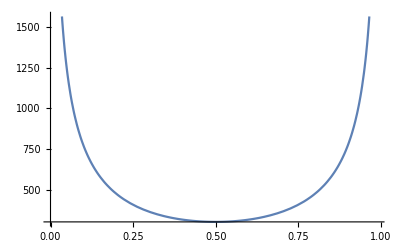

```mathematica
Plot[distribution[p,10000,0.00001,0.00001,0.0001]/91.81151630693743,{p,0.0001,0.99}]
```

```mathematica
distribution[p_,s_,u_,v_]= Exp[-s*p*(1-p)+2*v*Log[p]-2*u*Log[(1-p)]]/p(1-p)
```

(ⅇ^(-((1-p) p s)-2 u Log[1-p]+2 v Log[p]) (1-p))/p

```mathematica
mys=1/10000
mymut=0.00001
```

1/10000

0.00001

```mathematica
myN=1000
```

1000

```mathematica
normalizingconstant=NIntegrate[distribution[p,myN,mys,mymut,mymut],{p,0.0000001,0.9999}]
```

27509.6

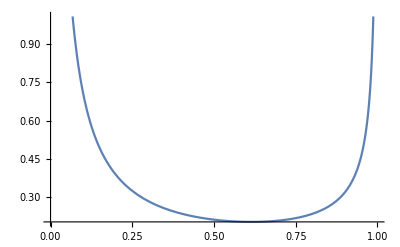

```mathematica
Plot[distribution[p,myN,mys,mymut,mymut]/normalizingconstant,{p,0.0000001,0.9999}]
```

```mathematica
var[p_]=2*100*p*(1-p)
```

200 (1-p) p

```mathematica
NIntegrate[var[p]*(distribution[p,myN,mys,mymut,mymut]/normalizingconstant),{p,0.001,0.999}]
```

9.85052